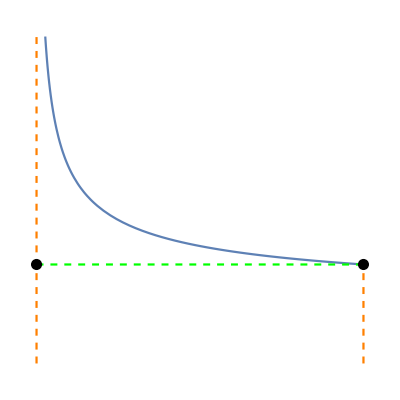

```mathematica
fx=Function[x,1/(x-0.5)^0.5+1];
f1=Plot[fx[x],{x,0.54,2},AxesOrigin-> {0,0},PlotRange-> All,AspectRatio->1,Epilog->{Disk[{2,fx[2]},Offset[4]],Disk[{0.5,fx[2]},Offset[4]]},Axes->False];
f2=ContourPlot[x==0.5,{x,0,1},{y,0,fx[0.54]},ContourStyle->{Orange,Dashed}];
f3=ContourPlot[x==2,{x,1,3},{y,0,fx[2]},ContourStyle->{Orange,Dashed}];
f4=Plot[fx[2],{x,0.5,2},PlotStyle->{Green,Dashed}];
Show[f1,f2,f3,f4]
```

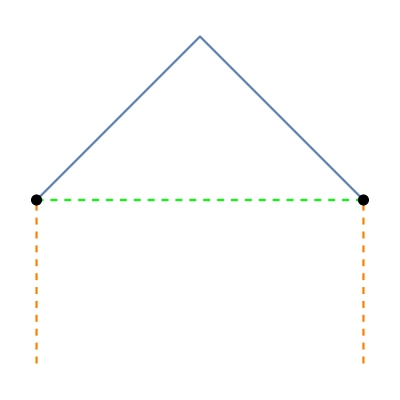

```mathematica
fx=Function[x,2-Abs[x-2]];
f1=Plot[fx[x],{x,1,3},AxesOrigin-> {0,0},PlotRange-> All,AspectRatio->1,Epilog->{Disk[{1,fx[1]},Offset[4]],Disk[{3,fx[3]},Offset[4]]},Axes->False];
f2=ContourPlot[x==1,{x,0,2},{y,0,fx[1]},ContourStyle->{Orange,Dashed}];
f3=ContourPlot[x==3,{x,2,4},{y,0,fx[3]},ContourStyle->{Orange,Dashed}];
f4=Plot[fx[3],{x,1,3},PlotStyle->{Green,Dashed}];
Show[f1,f2,f3,f4]
```

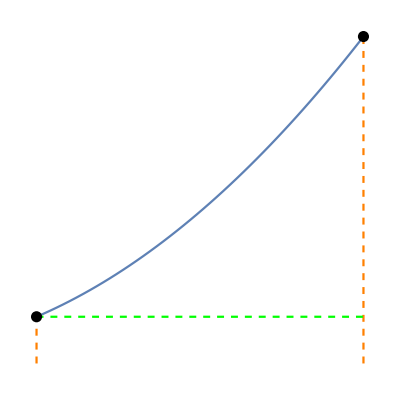

```mathematica
fx=Function[x,3x^2+1];
f1=Plot[fx[x],{x,1,3},AxesOrigin-> {0,0},PlotRange-> All,AspectRatio->1,Epilog->{Disk[{1,fx[1]},Offset[4]],Disk[{3,fx[3]},Offset[4]]},Axes->False];
f2=ContourPlot[x==1,{x,0,2},{y,0,fx[1]},ContourStyle->{Orange,Dashed}];
f3=ContourPlot[x==3,{x,2,4},{y,0,fx[3]},ContourStyle->{Orange,Dashed}];
f4=Plot[fx[1],{x,1,3},PlotStyle->{Green,Dashed}];
Show[f1,f2,f3,f4]
```

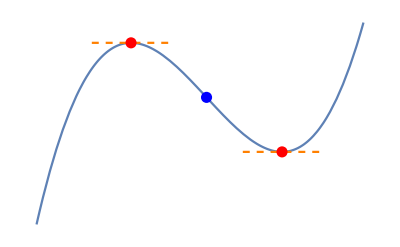

```mathematica
f2x=Function[x,(x-1)(x-2)(x-3)];
df2x=Function[x,D[f2x[x],x]];
df=Solve[df2x[x]==0,x];
d1=x/.df[[1]];
d2=x/.df[[2]];
ddf2x=Function[x,D[df2x[x],x]];
ddf=Solve[ddf2x[x]==0,x];
dd=x/.ddf[[1]];
p1=Plot[f2x[x],{x,0.7,3.2},Epilog-> {Red,Disk[{d1,f2x[d1]},Offset[4]],Disk[{d2,f2x[d2]},Offset[4]],Blue,Disk[{2,f2x[2]},Offset[4]]},Axes->False];
p2=Plot[f2x[d1],{x,d1-0.3,d1+0.3},PlotStyle->{Orange,Dashed}];
p3=Plot[f2x[d2],{x,d2-0.3,d2+0.3},PlotStyle->{Orange,Dashed}];
Show[p1,p2,p3]
```

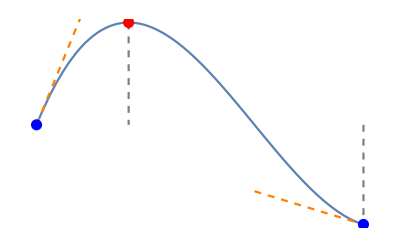

```mathematica
f3=Function[x,(x-1)(x-2)(x-3)];
df3=Function[x,D[f3[x],x]];
ddf3=Function[x,D[df3[x],x]];
sol=Solve[df3[x]==0,x];
rd1=x/.sol[[1]];
sol=Solve[ddf3[x]==0,x];
rdd=x/.sol[[1]];
p1=Plot[f3[x],{x,1,2.5},Epilog-> {Blue,Disk[{1,f3[1]},Offset[4]],Disk[{2.5,f3[2.5]},Offset[4]],Red,Disk[{rd1,f3[rd1]},Offset[4]]},Axes->False];
k1=df3[x]/.x->1;
k2=df3[x]/.x->2.5;
p2=Plot[k1*(x-1)+f3[1],{x,1,1.2},PlotStyle->{Orange,Dashed}];
p3=Plot[k2*(x-2.5)+f3[2.5],{x,2.,2.5},PlotStyle->{Orange,Dashed}];
p4=ContourPlot[x==rd1,{x,1,2},{y,0,f3[rd1]},ContourStyle->{Gray,Dashed}];
p5=ContourPlot[x==2.5,{x,2,3},{y,0,f3[2.5]},ContourStyle->{Gray,Dashed}];
Show[p1,p2,p3,p4,p5]
```

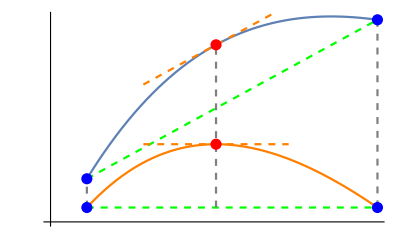

```mathematica
f2x=Function[x,(x-1)(x-2.6)^3(x-3)+0.2];
k=(f2x[1.4]-f2x[1])/0.4;
df2x=Function[x,D[f2x[x],x]];
df=Solve[df2x[x]==k,x];
d1=x/.df[[1]];
p1=Plot[f2x[x],{x,1,1.4},Epilog-> {Blue,Disk[{1,f2x[1]},Offset[4]],Disk[{1.4,f2x[1.4]},Offset[4]],Disk[{1,0},Offset[4]],Disk[{1.4,0},Offset[4]],Red,Disk[{d1,f2x[d1]},Offset[4]],Disk[{d1,f2x[d1]-k(d1-1)-0.2},Offset[4]]},AxesOrigin->{0.95,-0.1},AxesStyle->Directive[LightGray],Ticks->None];
p2=Plot[k(x-d1)+f2x[d1],{x,d1-0.1,d1+0.1},PlotStyle->{Orange,Dashed}];
p3=Plot[f2x[x]-k(x-1)-0.2,{x,1,1.4},PlotStyle->Orange];
p4=Plot[k*(x-1)+f2x[1],{x,1,1.4},PlotStyle->{Green,Dashed}];
p5=Plot[f2x[d1]-k(d1-1)-0.2,{x,d1-0.1,d1+0.1},PlotStyle->{Orange,Dashed}];
p6=Plot[f2x[1]-0.2,{x,1,1.4},PlotStyle->{Green,Dashed}];
p7=ContourPlot[x==1,{x,0,2},{y,0,f2x[1]},ContourStyle->{Gray,Dashed}];
p8=ContourPlot[x==1.4,{x,1,2},{y,0,f2x[1.4]},ContourStyle->{Gray,Dashed}];
p9=ContourPlot[x==d1,{x,0,2},{y,0,f2x[d1]},ContourStyle->{Gray,Dashed}];
Show[p1,p2,p3,p4,p5,p6,p7,p8,p9]
```

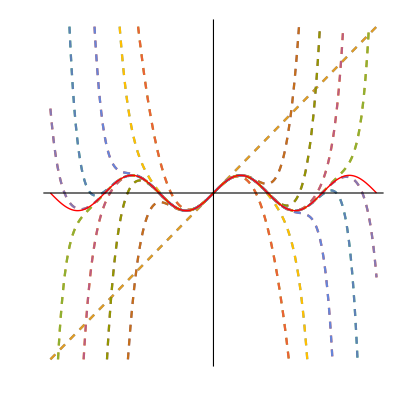

```mathematica
p1=Plot[Sin[x],{x,-3Pi,3Pi},PlotRange->{-4,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[Sin[x],{x,0,n}]],{n,20}]],{x,-3Pi,3Pi},AspectRatio->Automatic,PlotRange->{-3Pi,3Pi},PlotStyle->Dashed,Ticks->None];
Show[p2,p1]
```

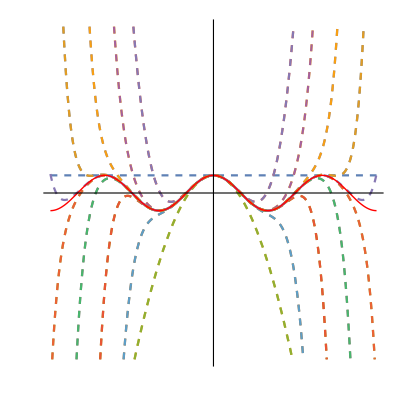

```mathematica
p1=Plot[Cos[x],{x,-3Pi,3Pi},PlotRange->{-4,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[Cos[x],{x,0,n}]],{n,20}]],{x,-3Pi,3Pi},AspectRatio->Automatic,PlotRange->{-3Pi,3Pi},PlotStyle->Dashed,Ticks->None];
Show[p2,p1]
```

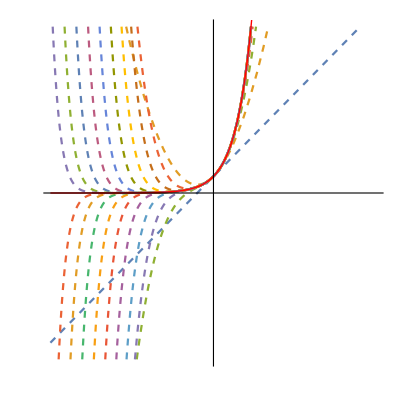

```mathematica
p1=Plot[E^x,{x,-10,10},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[E^x,{x,0,n}]],{n,20}]],{x,-10,10},AspectRatio->Automatic,PlotRange->{-10,10},PlotStyle->Dashed,Ticks->None];
Show[p2,p1]
```

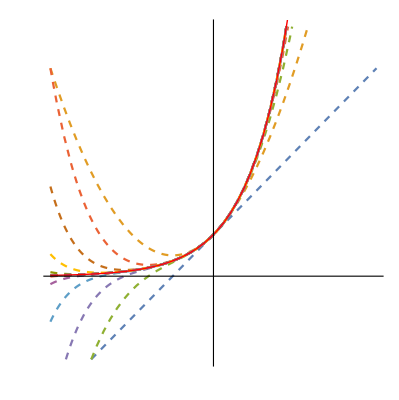

```mathematica
p1=Plot[E^x,{x,-4,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[E^x,{x,0,n}]],{n,20}]],{x,-4,4},AspectRatio->Automatic,PlotRange->{-2,6},PlotStyle->Dashed,Ticks->None];
Show[p2,p1]
```

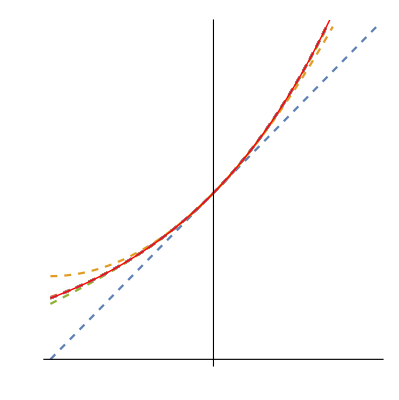

```mathematica
p1=Plot[E^x,{x,-1,1},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[E^x,{x,0,n}]],{n,20}]],{x,-1,1},AspectRatio->Automatic,PlotRange->{0,2},PlotStyle->Dashed,Ticks->None];
Show[p2,p1]
```

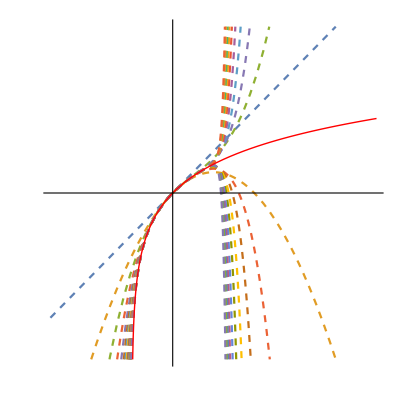

```mathematica
p1=Plot[Log[x+1],{x,-3,5},PlotRange->{-4,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[Log[x+1],{x,0,n}]],{n,20}]],{x,-3,5},AspectRatio->Automatic,PlotRange->{-4,4},PlotStyle->Dashed,Ticks->None];
Show[p2,p1]
```

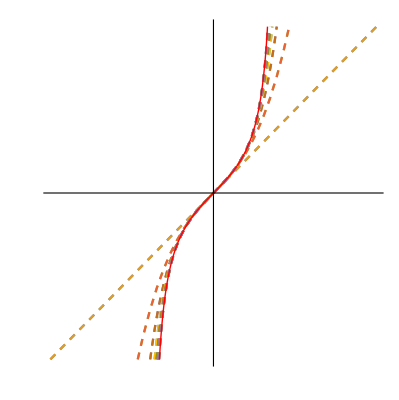

```mathematica
p1=Plot[Tan[x],{x,-Pi/2,Pi/2},PlotRange->{-4,4},PlotStyle->{Thick,Red},Exclusions->{-Pi/2,Pi/2}];
p2=Plot[Evaluate[Table[Normal[Series[Tan[x],{x,0,n}]],{n,20}]],{x,-4,4},AspectRatio->Automatic,PlotRange->{-4,4},PlotStyle->Dashed,Ticks->None];
Show[p2,p1]
```

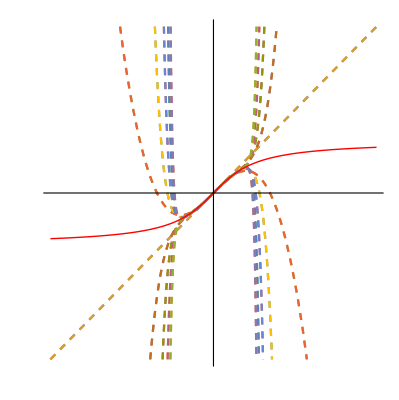

```mathematica
p1=Plot[ArcTan[x],{x,-5,5},PlotRange->{-4,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[ArcTan[x],{x,0,n}]],{n,20}]],{x,-5,5},AspectRatio->Automatic,PlotRange->{-5,5},PlotStyle->Dashed,Ticks->None];
Show[p2,p1]
```

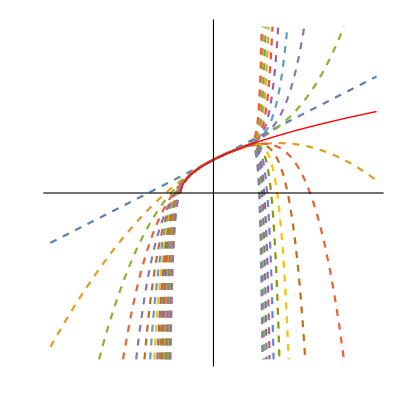

```mathematica
p1=Plot[(1+x)^{1/2},{x,-5,5},PlotRange->{-4,4},PlotStyle->{Thick,Red}];
p2=Plot[Evaluate[Table[Normal[Series[(1+x)^{1/2},{x,0,n}]],{n,20}]],{x,-5,5},AspectRatio->Automatic,PlotRange->{-5,5},PlotStyle->Dashed,Ticks->None];
Show[p2,p1]
```

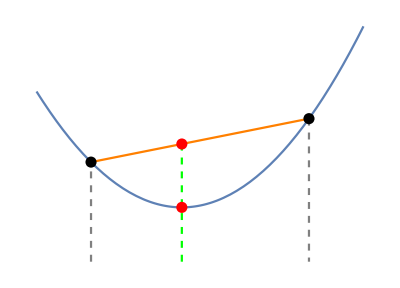

```mathematica
f=Function[x,x^2-2x+1.3];
k=(f[1.7]-f[0.5])/1.2;
p1=Plot[f[x],{x,0.2,2},AxesOrigin->{0.3,0},AspectRatio->Automatic,Epilog->{Disk[{0.5,f[0.5]},Offset[4]],Disk[{1.7,f[1.7]},Offset[4]],
Red,Disk[{1,f[1]},Offset[4]],Disk[{1,k(1-0.5)+f[0.5]},Offset[4]]},Axes->False];
p2=Plot[k(x-0.5)+f[0.5],{x,0.5,1.7},PlotStyle->{Orange}];
p3=ContourPlot[x==0.5,{x,0,1},{y,0,f[0.5]},ContourStyle->{Gray,Dashed}];
p4=ContourPlot[x==1.7,{x,1,2},{y,0,f[1.7]},ContourStyle->{Gray,Dashed}];
p5=ContourPlot[x==1,{x,0,2},{y,0,k(1-0.5)+f[0.5]},ContourStyle->{Green,Dashed}];
Show[p1,p2,p3,p4,p5]
```

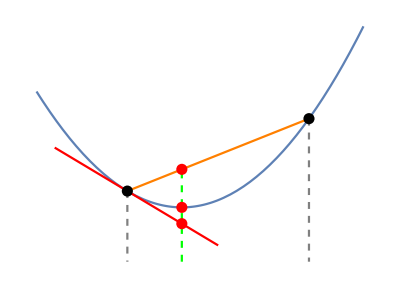

```mathematica
f=Function[x,x^2-2x+1.3];
df=Function[x,D[f[x],x]];
k=(f[1.7]-f[0.7])/1;
k1=df[x]/.x-> 0.7;
p1=Plot[f[x],{x,0.2,2},AxesOrigin->{0.3,0},AspectRatio->Automatic,Epilog->{Disk[{0.7,f[0.7]},Offset[4]],Disk[{1.7,f[1.7]},Offset[4]],
Red,Disk[{1,f[1]},Offset[4]],Disk[{1,k(1-0.7)+f[0.7]},Offset[4]],Disk[{1,k1(1-0.7)+f[0.7]},Offset[4]]},Axes->False];
p2=Plot[k(x-0.7)+f[0.7],{x,0.7,1.7},PlotStyle->{Orange}];
p3=ContourPlot[x==0.7,{x,0,1},{y,0,f[0.7]},ContourStyle->{Gray,Dashed}];
p4=ContourPlot[x==1.7,{x,1,2},{y,0,f[1.7]},ContourStyle->{Gray,Dashed}];
p5=ContourPlot[x==1,{x,0,2},{y,0,k(1-0.7)+f[0.7]},ContourStyle->{Green,Dashed}];
p6=Plot[k1(x-0.7)+f[0.7],{x,0.3,1.2},PlotStyle->{Red}];
Show[p1,p2,p3,p4,p5,p6]
```